## Graphing Parametric Equations

Exercise 1:  Use Mathematica to confirm that T[π] has unit length and that it is orthogonal to r[π].

```mathematica
r[t_] := {Cos[3t]+ 2Cos[t],Sin[3t],Sin[3t]}
```

```mathematica
T[t_] := r'[t]/Norm[r'[t]]
```

Norm is equivalent to magnitude.

```mathematica
Norm[T[π]]
```

1

The dot product of the two vectors indicates that they are orthogonal.

```mathematica
T[π].r[π]
```

0

With work, one may graphically show the curve and the unit tangent vector at t = t0.  Note that the tanline below is a line starting at r[t0] with direction vector T[t0].

```mathematica
t0 = Pi/4;
Manipulate[curve=ParametricPlot3D[r[t],{t,0,2π},AspectRatio->Automatic]; 
tanline = ParametricPlot3D[r[t0] + t T[t0], {t,0,1},PlotStyle->Red];
tanpoint = Graphics3D[{PointSize[0.02],Point[r[t0]]}];
Show[curve,tanline,tanpoint],{t0,-π,π}]
```

Exercise 2:   
(a)  For the curve r[t_] = {Cos[3t]+ 2Cos[t],Sin[3t],Sin[3t]},  have Mathematica find the standard unit normal vector, which we’d normally represent by N(t).    Since N[ ] is a predefined Mathematica command, call the unit normal vector nn[t_]

```mathematica
r[t_] := {Cos[3t]+ 2Cos[t],Sin[3t],Sin[3t]}
T[t_] := r'[t]/Norm[r'[t]]
nn[t_]:=N[T'[t]/Norm[T'[t]]]//FunctionExpand
```

(b)   Find the exact value of the unit normal vector nn[t] at t = π/4, and find its numerical value to the default precision.   If you do not get a numerical value, try re-entering a value for T[t_] which does not involve unnecessary Abs[ ] commands, and calculate nn[t_] from there.

```mathematica
nn[π/4]
```

{0.646997,-0.539164,-0.539164}

Exercise 3:  
(a)  Modify the code above Exercise 2 to display the curve r[t_] = {Cos[3t]+ 2Cos[t],Sin[3t],Sin[3t]},   its unit tangent vector T[t] in red, and its unit normal vector nn[t] in green at t = π/4.
(b)  Repeat (a) for t = π.    
(c)  Repeat (a) for t = 6.  
                                    (I’ll need to see all 3 graphs to grade them.)

```mathematica
Column[Show[{ParametricPlot3D[{r[t]},{t,-Pi,Pi}],ParametricPlot3D[r[#] + t T[#],{t,0,1},PlotStyle->Red],ParametricPlot3D[r[#]+t*nn[#],{t,0,1},PlotStyle->Green], Graphics3D[{PointSize[0.02],Point[r[#]]}]},ImageSize-> Large]&/@{π/4,π,6}]
```

-Graphics3D-
-Graphics3D-
-Graphics3D-

Exercise 4:  For r[t_] = {Cos[3t]+ 2Cos[t],Sin[3t],Sin[3t]},  find the components of accelerations in the direction of unit tangent T[t] and in the direction of the standard unit normal N(t) using the formulas
a_T = a·T   and a_N = (‖v×a‖)/(‖v‖).

```mathematica
aT[t_]:=r''[t].T[t]
```

```mathematica
aN[t_]:=Norm[r'[t]×r''[t]]/Norm[r'[t]]//FunctionExpand
```

Exercise 5:  
(a)   Plot the functions
     r[t] = {Cos[3t]+ 2Cos[t],Sin[3t],Sin[3t]},
     s[t] = {Cos[3t]+ 2Cos[t],Sin[3t],0}, and
     u[t] = {Cos[3t]+ 2Cos[t],Sin[3t],t}, 
from t = 0 to t = 2π.

```mathematica
r[t_] := {Cos[3t]+ 2Cos[t],Sin[3t],Sin[3t]}
     s[t_]:= {Cos[3t]+ 2Cos[t],Sin[3t],0}
     u[t_]:= {Cos[3t]+ 2Cos[t],Sin[3t],t}
```

```mathematica
ParametricPlot3D[{r[t],s[t],u[t]},{t,0,2π},PlotLegends->"Expressions"]
```

-Graphics3D-

(b)  Compute and compare the arc lenghts of r[t], s[t], and u[t] for 0 ≤ t ≤ 2π.  Which is longest? Which is shortest?   Note:  You may want to use the NIntegrate command.

```mathematica
arc[f_,t_]:=NIntegrate[Norm[f'[q]],{q,0,t},MaxRecursion->20]
```

```mathematica
Grid[{"The arc length of "<>ToString[#]<>"[t] is ",arc[#,2π]}&/@{r,s,u}]
```

The arc length of r[t] is  | 23.9683
The arc length of s[t] is  | 20.0158
The arc length of u[t] is  | 21.0973

s is the smallest, u is the largest

(c)  Excute the the Mathematica code below and discuss what it shows.

```mathematica
r[t_] := {Cos[3t]+2Cos[t],  Sin[3t], Sin[3t]};
s[t_] := {Cos[3t]+2Cos[t],  Sin[3t],  0};
ParametricPlot3D[{r[t],s[t]},{t,0,2π}, ViewPoint->{4,0,0}]
```

-Graphics3D-

In r[t], there is a factor adding to the z component. This causes that graph to increase in the z direction.

(d)  Viewing the 2D output from the code of part (b), the 45-degree line produced by r[t] is √2 times as long as the horizontal line produced by s[t].  Is the arc length of r[t] also √2 times the arc length of  s[t] ?

```mathematica
If[N[√2]arc[s,2π]==arc[r,2π],"r[t] has the same arc length as s[t]","r[t] does not have the same arc length as s[t]"]
```

r[t] does not have the same arc length as s[t]

## Plotting Surfaces

Exercise 6:  Recall from class that for f(x,y) = (x^2-y^2)/(x^2+y^2)  ,   the limit as (x,y) approaches (0,0) does not exist.  
(a)  Provide a written description of why this limit does not exist based on a plot of this function on an appropriate domain near the origin, rotated to an appropriate viewing angle to assist your argument.

```mathematica
Column[Show[Plot3D[(x^2-y^2)/(x^2+y^2),{x,-5,5},{y,-5,5},PlotRange->{-1.1,1.1},ViewPoint->#],ImageSize-> Large]&/@{{1,0,0},{0,1,0},{1.1,1.1,0}}]
```

-Graphics3D-
-Graphics3D-
-Graphics3D-

In the first example, as (x,y) approaches (0,0), it appears that z approaches 1, but as (x,y) approaches (0,0) in the second example, it appears that z approaches -1.

(b)  Provide a written description of why this limit does not exist based a contour plot for this function near the origin.

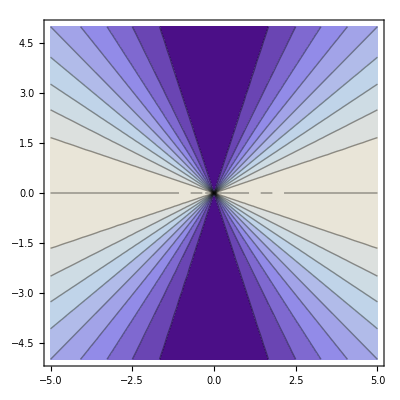

```mathematica
ContourPlot[(x^2-y^2)/(x^2+y^2),{x,-5,5},{y,-5,5}]
```

z has many values as each section approaches the origin. As is visible with this contour plot, there are many z values for each (x,y) line.